#### Reference

https : // arxiv . org/pdf/physics/9902072. pdf

#### Constants

```mathematica
mm=10^(-3);μK =10^(-6);μm=10^(-6);THz=1000000000000;MHz=10^6;
m=1.4192261*10^(-25); (*Rb atom mass in Kg*)
ℏ=1.054571817*10^(−34); (*Planck constant in SI*)
kb=1.380649*10^(-23); (*Boltzmann constant in SI*)
α=10.9*10^(-39);(*polarizability of Rb ground state @1064nm*)
c=3*10^8;(*Speed of light*)
ϵo = 8.8542*10^(-12);(*Vacuum permitivity*)
```

#### Phase space density

```mathematica
No=9.3*10^8; (*no. of atoms in atomic cloud*)
T=40.6 μK; (*Temperature of atomic cloud*)
σ=1.0mm; (*gaussian size of atomic cloud*)

ngauss=No/(Power[2*Pi,0.5]*σ)^3 (*1/m^3*)
PSD=ngauss*Power[2*Pi*ℏ*ℏ/(m*kb*T),1.5]*10^5
```

5.90491×10^16

0.153716

#### Trap Depth as a function of Laser Power

```mathematica
w=36μm;(*beam waist*)
ClearAll[Intensity,Udip,P]
Intensity[P_]=2*P/(Pi*w*w);
ωo = 2*Pi*377.1074635*THz;
ω = 2*Pi*281.759829*THz;
Γ =2*Pi*6.065*MHz;
ω /ωo;
Udip[P_]=-2*(3*Pi*c*c*Intensity[P]/(2ωo*ωo*ωo))((Γ/(ωo-ω))+(Γ/(ωo+ω)));
(*Cross trap = Single trap x2*)
```

#### Low, High and mean frequency

```mathematica
ωL=Power[4U/(m*w*w)]
ωH=Power[8U/(m*w*w)]
ωm=Power[ωL*ωL*ωH,1/3]
```

2.17472×10^34 U

4.34944×10^34 U

2.73998×10^34 (U^3)^(1/3)

#### Potential depth in terms Temperature

In experiment we are roughly starting with 10 x Peak depth (Since not all atom has the minimum velocity and not all of them are exactly at the center, finite size)

```mathematica
P=15; (*optical power*)
Temp=-(1000000)Udip[P]/kb (*Potential depth in terms of temperature (μK)*)
```

2477.88

#### Potential depth vs . Power

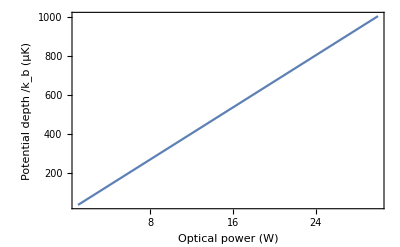

```mathematica
Plot[-(1000000)Udip[x]/kb ,{x,1,30},PlotRange->All,Frame->True,FrameLabel->{"Optical power (W)","Potential depth /k_b (μK)"}]
```

### AOD Teloscope config

Focus waist

```mathematica
nm=10^(-9);
f1=125mm;f2=350mm;f3=300mm;w0=1mm;λ=1064nm;
angle=1;(*Total angle*)
wf=1000000*N[λ*f1*f3/(Pi*w0*f2)](*Focused beam waist in micro meter*)
h0=N[f1*Tan[angle/2]]
```

36.2873

0.0682878